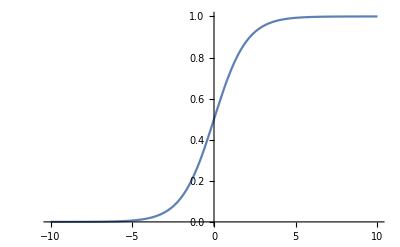

```mathematica
fsigmoid[x_]:=1/(Exp[-x]+1);(*シグモイド関数*)
(*test*)
Plot[fsigmoid[x],{x,-10,10}]
```

```mathematica
(*fout: 前の層の出力vxから次の層の出力を計算する関数。mWはリンクの重み行列(行列なので先頭にmをつけた)*)
```

```mathematica
fout[mW_List,vx_List]:=Module[{vu,vy},
vu=mW.vx;(*リンクの重みmWと前層の出力の行列積で各unitに入る活性ベクトルを計算*)
vy=Map[fsigmoid,vu];(*vuの各成分をsigmoid関数に入れて出力計算*)
Return[vy];
];
```

```mathematica
fout[{{w11,w12},{w21,w22}},{x1,x2}]
```

{1/(1+ⅇ^(-w11 x1-w12 x2)),1/(1+ⅇ^(-w21 x1-w22 x2))}

```mathematica
fforward[vx_]:=Module[{},(*作業用変数はないので作業用変数のリストは空リスト*)
gvy1=fout[gW1,vx];(*隠れ層(第1unit層)の出力計算*)
gvy2=fout[gW2,gvy1];(*出力層(第2unit層)の出力計算*)
Return[gvy2];(*出力層の出力がNNとしての出力*)
];
```

```mathematica
(*記号計算を使ったtest。入力unit2つ。隠れ層unit3つ、出力unit2つの場合*)
gW1={{a11,a12},{a21,a22}};
gW2={{b11,b12},{b21,b22}};
fforward[{x1,x2}](*NNとしての出力(=出力層の出力)*)
```

{1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2)))),1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))}

```mathematica
gvy1(*隠れ層の出力。fforwardでセットされた値を確かめる。*)
```

{1/(1+ⅇ^(-a11 x1-a12 x2)),1/(1+ⅇ^(-a21 x1-a22 x2))}

```mathematica
fbackward[vx_List,vy1_List,vy2_List,vt_List,eta_]:=Module[{vs2,vs1,mp2,mp1},
vs2=(vy2-vt)*(vy2*(1-vy2));(*誤差(vy2-vt)の「unit層2逆伝播」*)
vs1=(vs2.gW2)*vy1*(1-vy1);(*「link層2とunit層1を逆伝播」。vy1には直前の前方計算で得たgvy1の値を入れること*)
gW2=gW2-eta*Outer[Times,vs2,vy1];(*gW2の調整*)
gW1=gW1=eta*Outer[Times,vs1,vy1];(*gW1の調整*)
(*結果はグローバル変数gW1,gW2に残るので、返値はなし*)
];
```

```mathematica
(*記号計算を使った簡単なtest*)
Clear[c1,c2];gW1={{a11,a12},{a21,a22}};
gW2={{b11,b12},{b21,b22}};
vx={a1,a2};gvw={c1,c2};gvy1={b1,b2};gvt={d1,d2};
fbackward[vx,gvy1,gvy2,gvt,eta];
Print[MatrixForm[gW2]];
  Print[MatrixForm[gW1]];(*結果はグローバル変数gW32,gW21に残る*)
```

(b11-(b1 (1-1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) (-d1+1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) eta)/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2)))) | b12-(b2 (1-1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) (-d1+1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) eta)/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))
b21-(b1 (1-1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) (-d2+1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) eta)/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2)))) | b22-(b2 (1-1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) (-d2+1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) eta)/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2)))))

((1-b1) b1^2 ((b11 (1-1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) (-d1+1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))+(b21 (1-1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) (-d2+1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) eta | (1-b1) b1 b2 ((b11 (1-1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) (-d1+1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))+(b21 (1-1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) (-d2+1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) eta
b1 (1-b2) b2 ((b12 (1-1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) (-d1+1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))+(b22 (1-1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) (-d2+1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) eta | (1-b2) b2^2 ((b12 (1-1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))) (-d1+1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2))))+(b22 (1-1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) (-d2+1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))))/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))) eta)